```mathematica
If[FreeQ[$Path, NotebookDirectory[]], 
	 PrependTo[$Path, NotebookDirectory[]]];
ClearAll["`*"];
<<llps`
<<Charu`
```

## Liquid-liquid phase separation

### Common-tangent construction

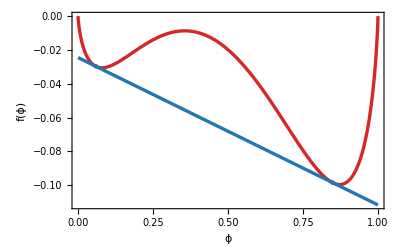

```mathematica
g=Module[{n=2,χ=2, ϕ1, ϕ2},
{ϕ1,ϕ2}=binodalPhi[n, χ];
Plot[{fhFree[ϕ, n, χ],
		fhMu[ϕ1, n, χ]ϕ + fhPi[ϕ1, n, χ]},
		{ϕ,0,1},
		Mesh->{{ϕ1,ϕ2}},
		MeshStyle->PointSize[Medium],
		FrameLabel->{"\!\(ϕ\)","\!\(f(ϕ)\)"},
		PlotTheme->"Charu"]]
Export["tangent.pdf",g];
```

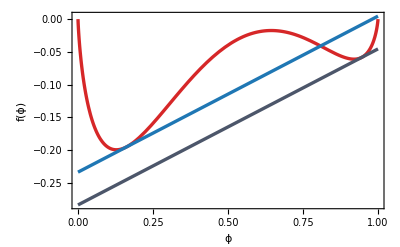

```mathematica
g=Module[{n=0.5,χ=4, ϕ1, ϕ2},
{ϕ1,ϕ2}=binodalPhi[n, χ,0.05];
Plot[{fhFree[ϕ, n, χ],
		fhMu[ϕ1, n, χ]ϕ + fhPi[ϕ1, n, χ],
		fhMu[ϕ2, n, χ]ϕ + fhPi[ϕ2, n, χ]},
		{ϕ,0,1},
		MeshStyle->PointSize[Medium],
		FrameLabel->{"\!\(ϕ\)","\!\(f(ϕ)\)"},
	PlotTheme->"Charu"]]
```

```mathematica
Export["~/projects/llps/partang_.pdf",g]
```

~/projects/llps/partang_.pdf

### Phase diagram

```mathematica
points=Module[{n=2, χMax=3}, binodal[n, χMax, "NumPoints"->200, "FudgeFactor"->0.0005]];
```

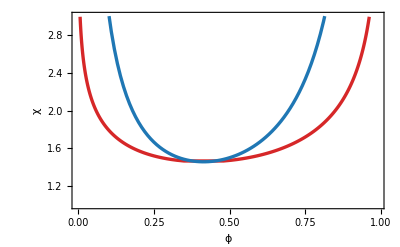

```mathematica
g=Module[{n=2},ListPlot[
	{points,
	Table[{ϕ,(-1+ϕ-n ϕ)/(2 n (-1+ϕ) ϕ)},{ϕ, 10^-10, 1-10^-10, 0.01}]},
	Joined->True,
	MeshStyle->None,
	PlotTheme->"Charu",
	PlotRange->{1,3},
	FrameLabel->{"\!\(ϕ\)","\!\(χ\)"}
]]
Export["phasediag.pdf",g];
```

```mathematica
1/(1+√2)//N
```

0.414214

## LLPS with elastic network

### Physical parameters

```mathematica
kB = 1.380649 10^-23;
vA=3.7 10^-28;
vB=4.8 10^-26;
n=vA/vB;
ϕSat[T_]:=(0.0467 T +1.728)/100;
χ[T_]:=-(((1-vA/vB)(1-ϕSat[T])+Log[ϕSat[T]])/(1-ϕSat[T])^2);
getT[c_]:=Quiet[T/.FindRoot[χ[T]==c,{T,10},WorkingPrecision->50]];
```

#### Radius estimates

```mathematica
Simplify[Solve[Evaluate[D[3Γ(1/r-β r0^2/r^3)+3G(5/6-1/(r/r0)-1/(3(r/r0)^3)),r]]==0,r],{G>0,r0>0,Γ>G r0}]
```

```mathematica
Simplify[Solve[Evaluate[D[3Γ(1/r-β r0^2/r^3)+6 G/(r/r0)(1-1/(r/r0))^2,r]]==0,r],{G>0,r0>0,Γ>G r0}]
```

```mathematica
{{r->(r0 (4 G r0-√(4 G^2 r0^2+6 G r0 (-1+β) Γ+3 β Γ^2)))/(2 G r0+Γ)},{r->(r0 (4 G r0+√(4 G^2 r0^2+6 G r0 (-1+β) Γ+3 β Γ^2)))/(2 G r0+Γ)}}/.{β->1}
```

{{r→(r0 (4 G r0-√(4 G^2 r0^2+3 Γ^2)))/(2 G r0+Γ)},{r→(r0 (4 G r0+√(4 G^2 r0^2+3 Γ^2)))/(2 G r0+Γ)}}

```mathematica
Clear[Γ]
```

```mathematica
{{r->(r0 (2 G r0-√(4 G^2 r0^2-12 G r0 β Γ+3 β Γ^2)))/(4 G r0-Γ)},{r->(r0 (2 G r0+√(4 G^2 r0^2-12 G r0 β Γ+3 β Γ^2)))/(4 G r0-Γ)}}
```

{{r→(r0 (2 G r0-√(4 G^2 r0^2+0.000048 β-0.048 G r0 β)))/(-0.004+4 G r0)},{r→(r0 (2 G r0+√(4 G^2 r0^2+0.000048 β-0.048 G r0 β)))/(-0.004+4 G r0)}}

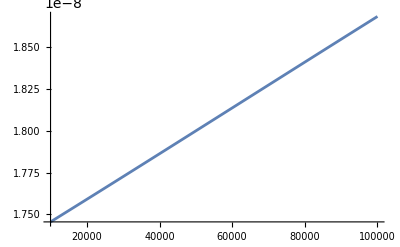

```mathematica
Plot[(r0 (4 G r0+√(4 G^2 r0^2+3 Γ^2)))/(2 G r0+Γ)/.{r0->10^-8,Γ->0.004,β->1},{G,10^4,10^5}]
```

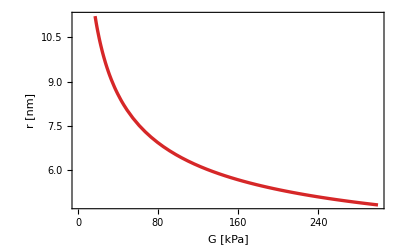

```mathematica
Plot[10^9((k T)/G)^(1/3) √((G^(2/3) (k T)^(1/3)+3 β Γ)/(-G^(2/3) (k T)^(1/3)+Γ))/.{T->273+45,Γ->0.004,k->kB,β->1,G->10^3 x},
		{x,0,300},
		FrameLabel->{"\!\(G\) [kPa]","\!\(r\) [nm]"},
		PlotTheme->"Charu"]
```

#### Tangent construction

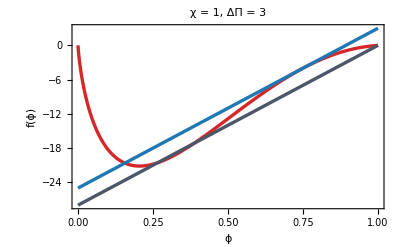

```mathematica
g=Module[{χ=1/n, ϕ1, ϕ2},
{ϕ1,ϕ2}=binodalPhi[n, χ, 3];
Plot[{fhFree[ϕ, n, χ],
		fhMu[ϕ1, n, χ]ϕ + fhPi[ϕ1, n, χ],
		fhMu[ϕ2, n, χ]ϕ + fhPi[ϕ2, n, χ]},
		{ϕ,0,1},
		MeshStyle->PointSize[Medium],
		FrameLabel->{"\!\(ϕ\)","\!\(f(ϕ)\)"},
		PlotLabel->"χ = 1, ΔΠ = 3",
	PlotTheme->"Charu"]]
```

#### Phase diagram

```mathematica
p1=Module[{points, χMax=3/n}, 
				points = binodal[n, χMax, "NumPoints"->100, "FudgeFactor"->0.01];
				points[[All,2]]=n points[[All,2]];
				points
];
```

```mathematica
p2=Module[{points, χMax=3/n, dP=0.25}, 
				points = binodal[n, χMax, dP, "NumPoints"->100, "FudgeFactor"->0.15];
				points[[All,2]]=n points[[All,2]];
				points
];
```

```mathematica
p3=Module[{points, χMax=3/n, dP=2.5}, 
				points = binodal[n, χMax, dP, "NumPoints"->100, "FudgeFactor"->0.15];
				points[[All,2]]=n points[[All,2]];
				points
];
```

```mathematica
p4=Module[{points, χMax=3/n, dP=25}, 
				points = binodal[n, χMax, dP, "NumPoints"->100, "FudgeFactor"->0.1];
				points[[All,2]]=n points[[All,2]];
				points
];
```

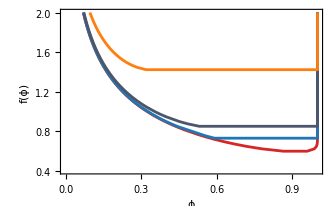

```mathematica
g=Module[{n=2},ListPlot[
	{p1,p2,p3,p4},
	Joined->True,
	MeshStyle->None,
	PlotTheme->"Charu",
	PlotRange->{0.4,2.},
	FrameLabel->{"\!\(ϕ\)","\!\(f(ϕ)\)"}
]]
```

```mathematica
Export["~/projects/llps/figures/phase1_.pdf",g]
```

~/projects/llps/figures/phase1_.pdf

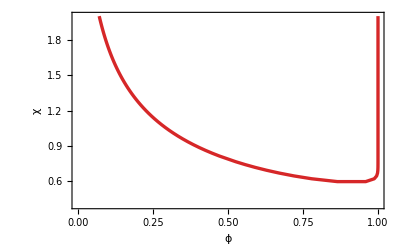

```mathematica
g=Module[{n=2},ListPlot[
	{p1},
	Joined->True,
	MeshStyle->None,
	PlotTheme->"Charu",
	PlotRange->{0.4,2.},
	FrameLabel->{"\!\(ϕ\)","\!\(χ\)"}
]]
```

Temperature version

```mathematica
p1T = p1;
p1T[[All,2]]=Quiet[getT/@p1T[[All,2]]];
p2T= p2;
p2T[[All,2]]=Quiet[getT/@p2T[[All,2]]];
p3T= p3;
p3T[[All,2]]=Quiet[getT/@p3T[[All,2]]];
p4T= p4;
p4T[[All,2]]=Quiet[getT/@p4T[[All,2]]];
```

Set::partd: Part specification p2T⟦All,2⟧ is longer than depth of object.

Set::partd: Part specification p3T⟦All,2⟧ is longer than depth of object.

Set::partd: Part specification p4T⟦All,2⟧ is longer than depth of object.

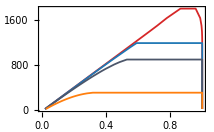

```mathematica
g=Module[{n=2},ListPlot[
	{p1T,p2T,p3T,p4T},
	Joined->True,
	MeshStyle->None,
	PlotTheme->"Charu",
	PlotRange->Full,
	FrameLabel->{"\!\(ϕ\)","\!\(T\)  [Celsius]"}
]]
```

```mathematica
Export["~/projects/llps/figures/phase2_.pdf",g]
```

~/projects/llps/figures/phase2_.pdf

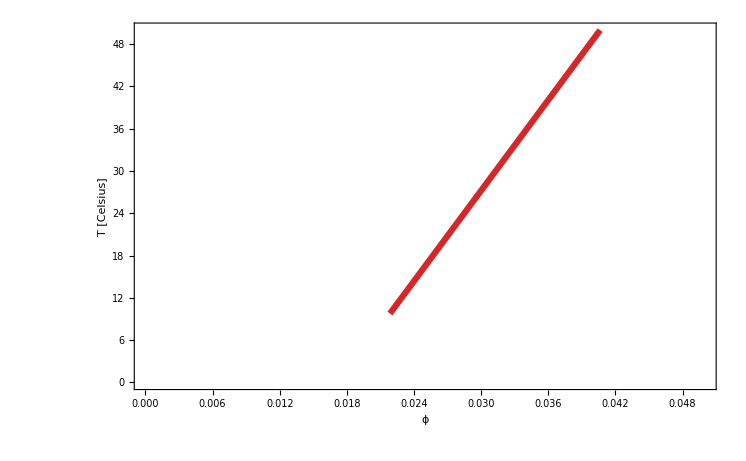

```mathematica
g=Module[{n=2},ListPlot[
	{p1T},
	Joined->True,
	MeshStyle->None,
	PlotTheme->"Charu",
PlotRange->{{0,0.05},{0,50}},
	PlotRange->Full,
	FrameLabel->{"\!\(ϕ\)","\!\(T\)  [Celsius]"}
]]
```

## Polydispersity

```mathematica
Integrate[4π Γ (x^2-r0^2)Exp[-(x-r)^2/σ^2],{x,0,∞}]
```

ConditionalExpression[π Γ (2 ⅇ^(-r^2/σ^2) r σ^2+(√π (2 r^2-2 r0^2+σ^2))/(√(1/σ^2))+√π σ (2 r^2-2 r0^2+σ^2) Erf[r/σ]), Re[σ^2]≥0]

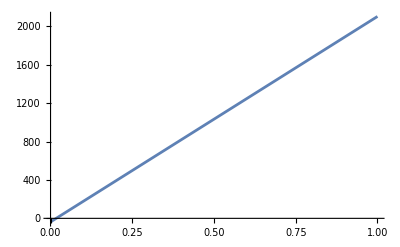

```mathematica
Plot[(ϕ-0.01728)/0.000467,{ϕ,0,1},PlotRange->Full]
```

```mathematica
1/0.000467
```

2141.33

```mathematica
1500/.8
```

1875.

```mathematica
D[fhFree[ϕ,χ,n],ϕ]
```

```mathematica
Solve[-1+n (1-ϕ)-n ϕ+1/χ-Log[1-ϕ]+Log[ϕ]/χ==0,χ]
```

{{χ→(1+Log[ϕ])/(1-n+2 n ϕ+Log[1-ϕ])}}

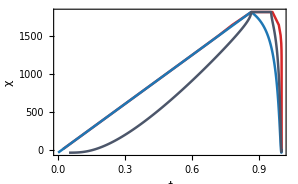

```mathematica
g=Module[{n=2},ListPlot[
	{p1T,pxT,psT},
	Joined->True,
	MeshStyle->None,
	PlotTheme->"Charu",
	FrameLabel->{"\!\(ϕ\)","\!\(χ\)"}
]]
```

```mathematica
Export["~/projects/llps/figures/phase2_.pdf",g]
```

~/projects/llps/figures/phase2_.pdf

```mathematica
Export["~/projects/llps/phase0_.pdf",g]
```

~/projects/llps/phase0_.pdf

```mathematica
px=({#,-((1-n)(1-#)+Log[#])/(1-#)^2}&)/@Subdivide[10^-10,1-10^-10,1000];
```

```mathematica
ps=({#,1/2(1/#+n/(1-#))})&/@Subdivide[10^-10,1-10^-10,1000];
```

```mathematica
pxT=px;pxT[[All,2]]=Quiet[getT/@pxT[[All,2]]];
```

```mathematica
psT=ps;psT[[All,2]]=Quiet[getT/@psT[[All,2]]];
```

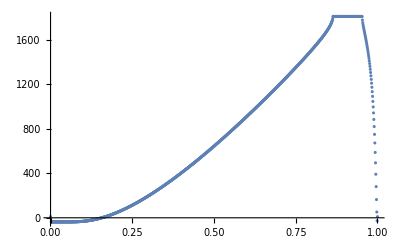

```mathematica
ListPlot[psT]
```

```mathematica
Subdivide[10^-10,2,100]
```

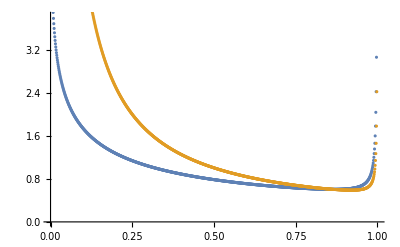

```mathematica
ListPlot[{px,ps}]
```

```mathematica
D[ϕ Log[ϕ]/m-(1-ϕ)Log[1-ϕ]+χ ϕ(1-ϕ),{ϕ,2}]
```

```mathematica
Solve[-1/(1-ϕ)+1/(m ϕ)-2 χ==0,χ]
```

{{χ→(-1+ϕ+m ϕ)/(2 m (-1+ϕ) ϕ)}}

```mathematica
n
```

0.00770833

```mathematica
α = √(1+0.03)
```

1.01489

```mathematica
3 α^2-3+Log[α^2]
```

0.119559

```mathematica
WolframAlpha["12 december 2021 to 18 january 2022"]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["21 november 2023 to 7 january 2024"]
```

WolframAlphaQueryResults